```mathematica
DSolve[y'[t]+2y[t]==1, y[t], t]
DSolve[{y'[t]+2y[t]==1, y[0]==-1}, y[t], t]
DSolve[{y'[t]+2y[t]==1, y[0]==0}, y[t], t]
DSolve[{y'[t]+2y[t]==1, y[0]==1}, y[t], t]
DSolve[{y'[t]+2y[t]==1, y[0]==2}, y[t], t]
DSolve[{y'[t]+2y[t]==1, y[0]==3}, y[t], t]
```

{{y[t]→1/2+ⅇ^(-2 t) C[1]}}

{{y[t]→1/2 ⅇ^(-2 t) (-3+ⅇ^(2 t))}}

{{y[t]→1/2 ⅇ^(-2 t) (-1+ⅇ^(2 t))}}

{{y[t]→1/2 ⅇ^(-2 t) (1+ⅇ^(2 t))}}

{{y[t]→1/2 ⅇ^(-2 t) (3+ⅇ^(2 t))}}

{{y[t]→1/2 ⅇ^(-2 t) (5+ⅇ^(2 t))}}

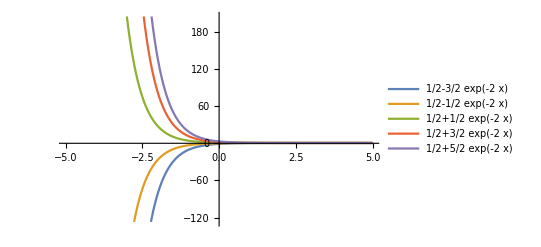

```mathematica
Plot[{(1/2)+(-3/2)Exp[-2x],(1/2)+(-1/2)Exp[-2x],(1/2)+(1/2)Exp[-2x], (1/2)+(3/2)Exp[-2x], (1/2)+(5/2)Exp[-2x]},{x,-5,5},PlotLegends->"Expressions"]
```

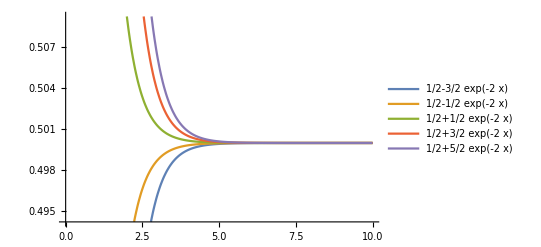

```mathematica
Plot[{(1/2)+(-3/2)Exp[-2x],(1/2)+(-1/2)Exp[-2x],(1/2)+(1/2)Exp[-2x], (1/2)+(3/2)Exp[-2x], (1/2)+(5/2)Exp[-2x]},{x,0,10},PlotLegends->"Expressions"]
```